{27.03,32.78,44.23,44.36,52.04,67.05,70.4,29.86,32.56,32.89,33.42,35.72,40.53,41.53,42.99,43.49,49.22,57.47,61.93}

7

{27.03,32.78,44.23,44.36,52.04,67.05,70.4}

{29.86,32.56,32.89,33.42,35.72,40.53,41.53,42.99,43.49,49.22,57.47,61.93}

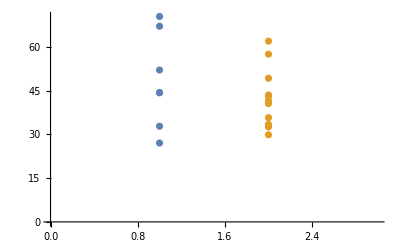

0.296004

0.296004

```mathematica
DataFromExcel=ToExpression[StringReplace[StringSplit[#,"\t"][[2]],","->""]]&/@StringSplit[NotebookGet[ClipboardNotebook[]][[1,1,1]],{"\n\n"}][[2;;]]
PosiSplit=Module[{return},
For[i=1,i≤Length[DataFromExcel]-1,i++,
If[DataFromExcel[[i]]>DataFromExcel[[i+1]],return=i];
];
return
]
Data1=DataFromExcel[[;;PosiSplit]]
Data2=DataFromExcel[[PosiSplit+1;;]]
ListPlot[{{1,#1}&/@Data1,{2,#1}&/@Data2},PlotRange->{{0,3},Automatic}]
TTest[{Data1,Data2}]
LocationEquivalenceTest[{Data1,Data2}]
```

```mathematica
ScientificForm[0.1077878603022471]
```

0.306261